# Nonlinear diffusion equation Support comes in new version of M.

```mathematica
ufun = NDSolveValue[{Div[{{-u[x]^2}}.Grad[u[x],{x}],{x}]== 4 + NeumannValue[2.,x==1],
DirichletCondition[u[x]==1.,x==0]},u,Element[{x},  Line[{{0},{1}}]]];
```

FindRoot::nosol: Linear equation encountered that has no solution.

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

```mathematica
Plot[ufun[x],{x,0,1}]
```

## Nonlinear Load Terms

```mathematica
Clear[u];
ufun = NDSolveValue[{ D[ u[x],{x,2}]==Sin[u[x]],DirichletCondition[u[x]==5.,x==0],DirichletCondition[u[x]==5.1,x==π/2]},u,{x}∈Line[{{0},{π/2}}]]
```

InterpolatingFunction[…]

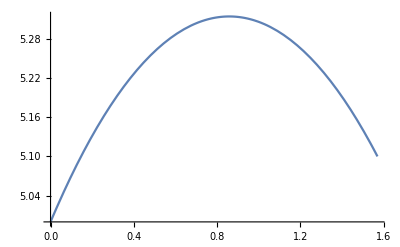

```mathematica
Plot[ufun[x],{x,0,π/2}]
```

```mathematica
ufun=NDSolveValue[{-D[u[x],{x,2}]==10,DirichletCondition[u[x]==-6ⅈ,x==0],
DirichletCondition[u[x]==-Sqrt[2]ⅈ,x==1]},u,{x}∈ Line[{{0},{1}}]]
```

InterpolatingFunction[…]

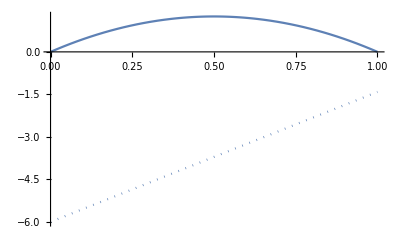

```mathematica
ReImPlot[ufun[x],{x,0,1}]
```

## Nonlinear Diffusion

```mathematica
NDSolveValue[{∇_{x} ×(-u[x]^2∇_{x} ×u[x])==4+NeumannValue[2.,x==1],
DirichletCondition[u[x]==1,x==0]},u[x],{x}∈Line[{{0},{1}}],
InitialSeeding-> {u[x]==1}]
```

InterpolatingFunction[…][x]

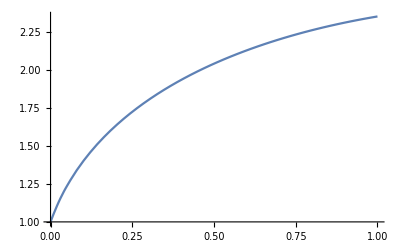

```mathematica
Plot[%,{x,0,1}]
```

```mathematica
NDSolveValue[{∇_{x}^2 u[x]+4u[x] D[u[x],x]==2,
DirichletCondition[u[x]==1,True]},u[x],{x}∈Line[{{0},{1}}],InitialSeeding->{u[x]==1}]
```

InterpolatingFunction[…][x]

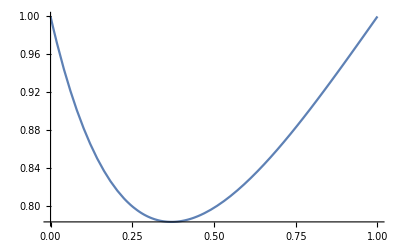

```mathematica
Plot[%,{x,0,1}]
```

## Radiation Boundary Condition

```mathematica
Ω=RegionDifference[Rectangle[],Disk[{1/2,1},1/4]];
```

```mathematica
eqn=∇_{x,y} .(-∇_{x,y} T[x,y])+T[x,y]-1==NeumannValue[-10^3T[x,y]^4,(1/4≤ x≤ 3/4)&&(y≥ 3/4)];
```

```mathematica
usol=NDSolveValue[{eqn,DirichletCondition[T[x,y]==1,x==0]},T,{x,y}∈Ω]
```

InterpolatingFunction[…]

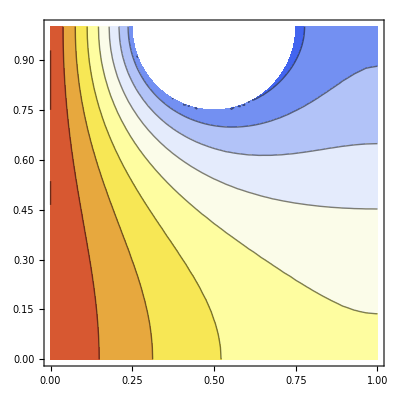

```mathematica
ContourPlot[usol[x,y],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap"]
```